1

1

1

2/25

{0,1,1/2,2/9,1/8,2/25,1/18,2/49,1/32,2/81,1/50}

{0,1,1/2,2/9,1/8,2/25,1/18,2/49,1/32,2/81,1/50}

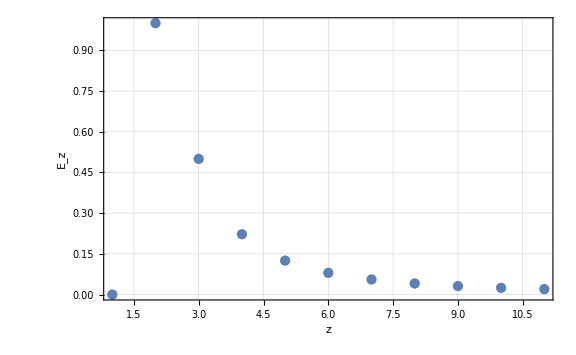

```mathematica
z=1;
R=1;
Integrate[(z-R u)/((R^2+z^2-2R z u)^(3/2)),{u,-1,1}]
1
Integrate[((z- R Cos[θ])Sin[θ])/((R^2+z^2-2 R z Cos[θ])^(3/2)),{θ,0,π}]
2/25
Table[Integrate[((z- R Cos[θ])Sin[θ])/((R^2+z^2-2 R z Cos[θ])^(3/2)),{θ,0,π}],{z,0,10}]
{0,1,1/2,2/9,1/8,2/25,1/18,2/49,1/32,2/81,1/50}
image= ListPlot[Table[Integrate[((z- R Cos[θ])Sin[θ])/((R^2+z^2-2 R z Cos[θ])^(3/2)),{θ,0,π}],{z,0,10,1}],PlotTheme->"Detailed",LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->24],FrameStyle->Directive[Black,Thick],FrameLabel->{Style[HoldForm["z"],26,Black],Style[HoldForm["E_z"],26,Black]},PlotRange->All,FrameTicksStyle->Directive[Black,18],ImageSize->Large,Mesh->Full]
```

```mathematica
Export["image1.png",image,ImageResolution->500]
```

image1.png